C[1]+x C[2]

{{C[1]→1.03833,C[2]→-1.1752,C[3]→-0.570418,ρ→-0.504748},{C[1]→1.54156,C[2]→-1.1752,C[3]→0.880645,ρ→-0.0015159},{C[1]→1.54157,C[2]→-1.1752,C[3]→0.866516,ρ→-0.00151481}}

1.03833-1.1752 x

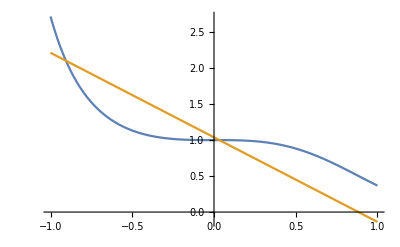

```mathematica
n=1;
a=-1;
b=1;
xi=Table[C[i],{i,n+1,2(n+1)}];
xi[[1]]=a;
xi[[n+2]]=b;
p[x_]=∑_(i=0)^n C[i+1] x^i
f[x_]=ⅇ^(-x^3);
Err[x_]=f[x]-p[x];
equ1=Table[Err[xi[[i]]]==(-1)^i ρ,{i,1,n+2}];
equ2=Table[Err'[xi[[i]]]==0,{i,2,n+1}];
equations=Flatten[{equ1,equ2}];
unknowns=Flatten[{Table[C[i],{i,1,2n+1}],ρ}];
solutions=NSolve[equations,unknowns,Reals]
ai=Flatten[Table[C[i],{i,1,n+1}]/.solutions];
P[x_]=∑_(i=0)^n ai[[i+1]] x^i
Plot[{f[x],P[x]},{x,a,b}]
```